```mathematica
Eigenvalues[({{2, -2}, {-2, 2}})]
```

{4,0}

{A→0.742795,α→0.6022}

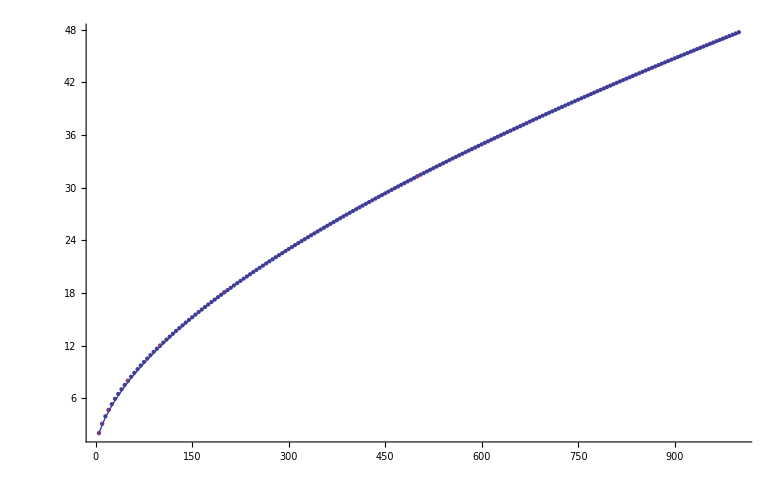

```mathematica
MD={{5,2.05},{10,3.11},{20,4.69},{50,8.01},{100,12.0},{200,18.1},{500,31.3}};
Σ[λ_]:=1/2(1/λ+1/(4+λ));
Ptot[c_,λ_]:=(2 λ Σ[λ])/c √(c+1)+(2 λ Σ[λ])/c+(4 c)/λ;
cm=Table[
FF=FindMinimum[{Ptot[c,λ],c>0},{c,1.0}];
{λ,c/.FF[[2]]}
,{λ,5,1000,5}];
FFF=FindFit[cm,A x^α,{A,α},x];
Print[FFF];
GrA=ListPlot[{cm,MD},PlotRange->All];
GrB=Plot[(A λ^α)/.FFF,{λ,5,1000},PlotRange->All];
Show[GrA,GrB]
```